## Calculate Mel Filterbank Parameters

#### First, we have some constants (e.g. the number of filters). We can vary these constants to tweak the filters

```mathematica
freqLowerbound = Quantity[20, "Hertz"];
freqUpperbound = Quantity[3, "Kilohertz"];
nFFT = 512;
sampleRate = Quantity[6, "Kilohertz"];
numFilters = 10;
```

#### Some functions to convert between hertz, mels, and DFT units

```mathematica
hertzToMel[f_] := 1125 * Log[1 + f / Quantity[700, "Hertz"]]
melToHertz[m_] := Quantity[700, "Hertz"] (Exp[m / 1125] - 1)
rescaleFreqBand[h_] := Floor[(nFFT + 1) * h / sampleRate]
```

#### Calculate linearly spaced mels between the lower and upper bounds, and then convert mels -> hertz -> DFT units

```mathematica
melLowerbound = hertzToMel[freqLowerbound];
melUpperbound = hertzToMel[freqUpperbound];
freqBandPeaks = Array[melToHertz, numFilters + 2, {melLowerbound, melUpperbound}];
rescaledFreqs = rescaleFreqBand /@ freqBandPeaks
```

{1,11,23,36,51,69,90,114,142,175,212,256}

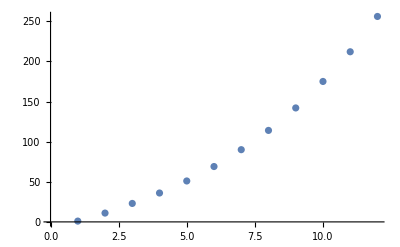

```mathematica
ListPlot[rescaledFreqs]
```

#### Finally, we can construct the mel filters

```mathematica
melFilter[m_] := With[
{f = rescaledFreqs},
Function[k, If[
k < f[[m]], 0, If[
k <= f[[m + 1]], (k - f[[m]]) / (f[[m + 1]] - f[[m]]), If[
k <= f[[m + 2]], (f[[m + 2]] - k) / (f[[m + 2]] - f[[m + 1]]), 0]]]]
]
```

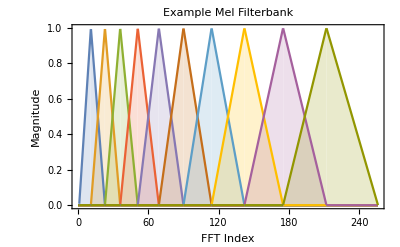

```mathematica
t = Table[melFilter[m][k], {m, 1, numFilters}];
Plot[t, {k, 0, nFFT / 2}, PlotRange-> All, Frame -> True, PlotLabel -> Style["Example Mel Filterbank", 24], FrameLabel-> {Style["FFT Index", 18], Style["Magnitude", 18]}, Filling -> Axis]
```